```mathematica
Clear["Global`*"]
```

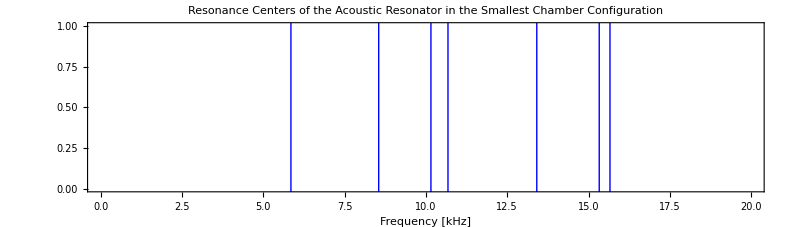

```mathematica
a=5.852;
c=8.55;
d=10.156;
e=10.68;
f=13.41;
g=15.33;
h=15.66;

plot1=Plot[{-1},{x,0,20},Frame->True,Epilog->{{Blue,Line[{{a,-5},{a,16}}]},{Blue,Line[{{c,-5},{c,16}}]},{Blue,Line[{{d,-5},{d,16}}]},{Blue,Line[{{e,-5},{e,16}}]},{Blue,Line[{{f,-5},{f,16}}]},{Blue,Line[{{g,-5},{g,16}}]},{Blue,Line[{{h,-5},{h,16}}]}},PlotRange->{0,1},ImageSize->{700,200},AspectRatio->Full,FrameLabel->{Style["Frequency [kHz]",FontSize->13],""},PlotLabel->Style["Resonance Centers of the Acoustic Resonator in the\nSmallest Chamber Configuration",FontSize->16]]
```

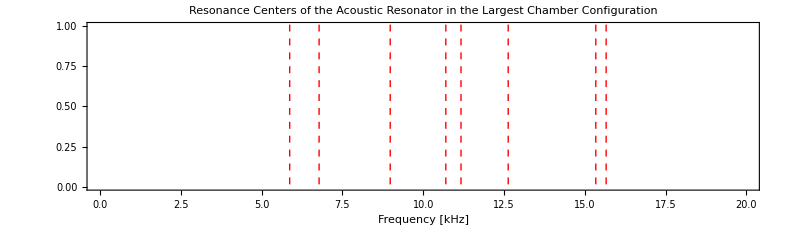

```mathematica
aa=5.87;
bb=6.78;
cc=8.98;
dd=10.7;
ee=11.17;
ff=12.63;
gg=15.34;
hh=15.66;

plot2=Plot[{-1},{x,0,20},Frame->True,Epilog->{{Red,Dashed,Line[{{aa,-5},{aa,16}}]},{Red,Dashed,Line[{{bb,-5},{bb,16}}]},{Red,Dashed,Line[{{cc,-5},{cc,16}}]},{Red,Dashed,Line[{{dd,-5},{dd,16}}]},{Red,Dashed,Line[{{ee,-5},{ee,16}}]},{Red,Dashed,Line[{{ff,-5},{ff,16}}]},{Red,Dashed,Line[{{gg,-5},{gg,16}}]},{Red,Dashed,Line[{{hh,-5},{hh,16}}]}},PlotRange->{0,1},ImageSize->{700,200},AspectRatio->Full,FrameLabel->{Style["Frequency [kHz]",FontSize->13],""},PlotLabel->Style["Resonance Centers of the Acoustic Resonator in the\nLargest Chamber Configuration",FontSize->16]]
```

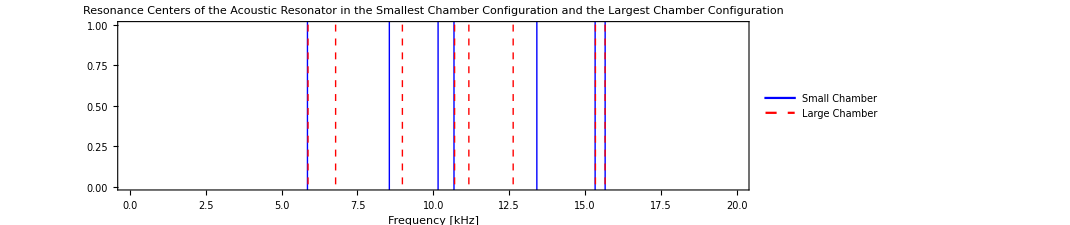

```mathematica
plot3=Plot[{-1},{x,0,20},Frame->True,Epilog->{{Blue,Line[{{a,-5},{a,16}}]},{Blue,Line[{{c,-5},{c,16}}]},{Blue,Line[{{d,-5},{d,16}}]},{Blue,Line[{{e,-5},{e,16}}]},{Blue,Line[{{f,-5},{f,16}}]},{Blue,Line[{{g,-5},{g,16}}]},{Blue,Line[{{h,-5},{h,16}}]},{Red,Dashed,Line[{{aa,-5},{aa,16}}]},{Red,Dashed,Line[{{bb,-5},{bb,16}}]},{Red,Dashed,Line[{{cc,-5},{cc,16}}]},{Red,Dashed,Line[{{dd,-5},{dd,16}}]},{Red,Dashed,Line[{{ee,-5},{ee,16}}]},{Red,Dashed,Line[{{ff,-5},{ff,16}}]},{Red,Dashed,Line[{{gg,-5},{gg,16}}]},{Red,Dashed,Line[{{hh,-5},{hh,16}}]}},PlotRange->{0,1},ImageSize->{700,200},AspectRatio->Full,PlotLegends->LineLegend[{Blue,{Dashed,Red}},{"Small Chamber","Large Chamber"}],FrameLabel->{Style["Frequency [kHz]",FontSize->13],""},PlotLabel->Style["Resonance Centers of the Acoustic Resonator in the\nSmallest Chamber Configuration and the Largest Chamber Configuration",FontSize->16]]
```